# Outliers Detection with Clustering

```mathematica
clustersNo = FindClusters[reducedOxyNo80[[All,1]],Method->"MeanShift"];
```

```mathematica
Dimensions[clustersNo]
```

{3}

```mathematica
Dimensions[clustersNo[[1]]]
Dimensions[clustersNo[[2]]]
Dimensions[clustersNo[[3]]]
```

{17,80}

{6,80}

{7,80}

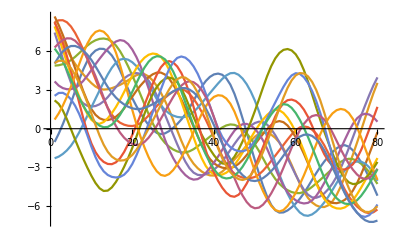
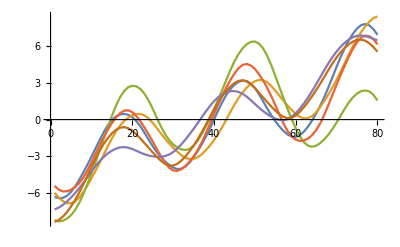
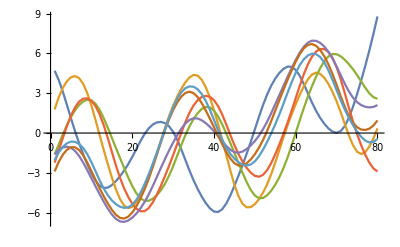
{-Graphics-→17,-Graphics-→6,-Graphics-→7}

```mathematica
Table[ListLinePlot[clustersNo[[i]]]-> Length[clustersNo[[i]]],{i,Dimensions[clustersNo][[1]]}]
```

Here i conclude that he found some otuliers

```mathematica
clusteredOxyNo = clustersNo[[1]];
```

```mathematica
clustersYes = FindClusters[reducedOxyYes80[[All,1]],Method->"MeanShift"];
Dimensions[clustersYes]
```

{5}

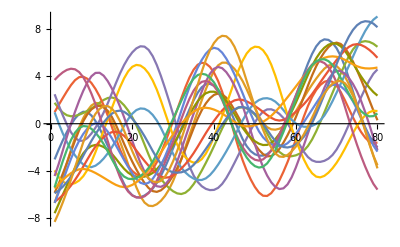
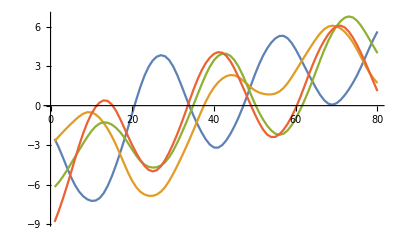
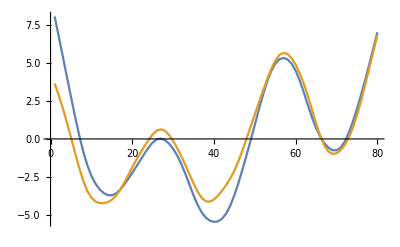
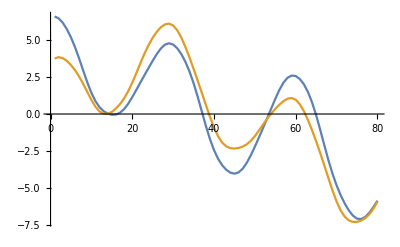
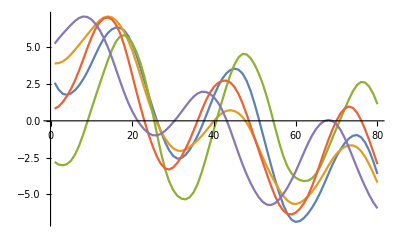
{-Graphics-→17,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→5}

```mathematica
Table[ListLinePlot[clustersYes[[i]]]-> Length[clustersYes[[i]]],{i,Dimensions[clustersYes][[1]]}]
```

```mathematica
clusteredOxyYes = Join[clustersYes[[1]],clustersYes[[2]]];
Dimensions[clusteredOxyYes]
ListLinePlot[clusteredOxyYes[[21]]]
```

{21,80}

```mathematica
clustData = Join[Table[clusteredOxyYes[[i]]->"Yes",{i,Length[clusteredOxyYes]}],Table[clusteredOxyNo[[i]]->"No",{i,Length[clusteredOxyNo]}]];
```

```mathematica
Dimensions[clustData]
```

{38}

{34}

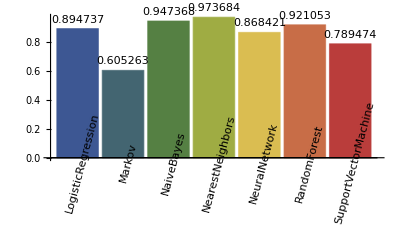

```mathematica
autoML[clustData]
```

```mathematica
autoMLAccurate[clustData]
```

$Aborted

## Archetypal on the reduced outliers set

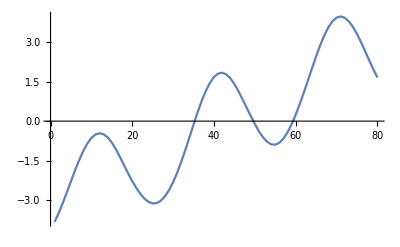

```mathematica
nooutMeanArchetypalYes = Mean[clusteredOxyYes[[All]]];
nooutMeanArchetypalNo = Mean[clusteredOxyNo[[All]]];
ListLinePlot[nooutMeanArchetypalYes]

l1DistVect[signal_List] := {ManhattanDistance[signal,nooutMeanArchetypalYes],ManhattanDistance[signal,nooutMeanArchetypalNo]}
```

```mathematica
dataDistArchDriftL1 = Join[Table[l1DistVect[clusteredOxyNo[[x]]]->"No",{x,Length[clusteredOxyNo]}],Table[l1DistVect[clusteredOxyYes[[x]]]->"Yes",{x,Length[clusteredOxyYes]}]];
```

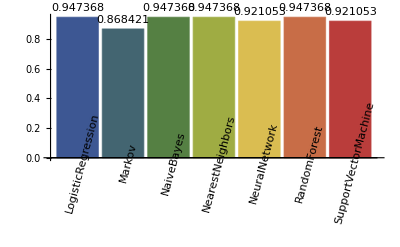

```mathematica
autoML[dataDistArchDriftL1]
```